```mathematica
<<FeynCalc`;
```

FeynCalc 10.1.0 (dev version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

# Definitions

## Defining different parameters, ALP models and the RG flow

```mathematica
DirectoryRoutines=FileNameJoin[{NotebookDirectory[],"notebooks"}]
```

/Users/thema/Downloads/WZW_axions_Git/notebooks

```mathematica
FileNameJoin[{DirectoryRoutines,"alp-models.nb"}]
```

/Users/thema/Downloads/WZW_axions_Git/notebooks/alp-models.nb

```mathematica
DirectoryRoutines=FileNameJoin[{NotebookDirectory[],"notebooks"}];
Print["Defining ALP models..."]
Block[{Print=Identity},
(*Parameters and functions*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-models.nb"}]];
];//AbsoluteTiming
Print["Defining baseline parameters and functions..."]
Block[{Print=Identity},
(*Parameters and functions*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"parameters-functions.nb"}]];
];//AbsoluteTiming
Print["Launching routines to compute/load running of the ALP couplings..."]
Block[{Print=Identity},
(*Running of ALP couplings*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-running.nb"}]];
];//AbsoluteTiming
```

Defining ALP models...

{0.183004,Null}

Defining baseline parameters and functions...

{0.366363,Null}

Launching routines to compute/load running of the ALP couplings...

{0.61828,Null}

## Defining ALP interactions with mesons

```mathematica
Print["Choice of the η-η' mixing angle:"]
θηηPrChoice= θηStandard
Print["Launching the notebook defining ChPT Lagrangian..."]
Block[{Print=Identity},
(*ChPT in SM*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"chpt-SM.nb"}]];
]//AbsoluteTiming
Print["Launching the notebook diagonalizing the quadratic Lagrangian with ALPs and mesons, and defining mixing angles..."]
Block[{Print=Identity},
(*ChPT with ALPs*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-diagonalization.nb"}]];
]//AbsoluteTiming
Print["Mass and kinetic mixing matrices between ALPs and mesons π^0, η, η':"]
Join[{{""},{"a"},{"π^0"},{"η"},{"η'"}},Join[{{"a","π^0","η","η'"}},Table[Mm0X[particle1,particle2],{particle1,listMesonP0a},{particle2,listMesonP0a}]],2]
Join[{{""},{"a"},{"π^0"},{"η"},{"η'"}},Join[{{"a","π^0","η","η'"}},Table[Km0X[particle1,particle2],{particle1,listMesonP0a},{particle2,listMesonP0a}]],2]
Print["ALP-meson mixing descriptions:"]
{#,mixingDescriptionMeaning[#]}&/@mixingDescriptionKeys
tabMixingAngles[description_,CU_,CD_,CS_,CG_]:={{"Meson","π_0","η","η'"},{"θ_(am^0)",θm0ALP["π^0",description],θm0ALP["η",description],θm0ALP["η'",description]}}/.{cu->CU,cd->CD,cs->CS,cG->CG}
Print["Selected mixing description:"]
choiceMixingDescription="O(δ,ϵ)"(*selectionDialogExplanationOneOption[mixingDescriptionKeys,mixingDescriptionMeaning[#]&/@mixingDescriptionKeys,"Select the description of the ALP-meson mixing",100]*)
tabMixingAngles[choiceMixingDescription,cu,cd,cs,cG]
ruleSymbolsToNumbersFinal[expr_,δorder_]:=ruleSymbolsToNumbers[expr,choiceMixingDescription,δorder]
Print["Generating the κ-invariant Lagrangian of the interaction of the ALPs with scalar, vector, and tensor mesons..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-SVT.nb"}]];
];//AbsoluteTiming
Print["Generating the final Lagrangian used to compute the widths (ChPT+ALP after performing the quadratic matrix diagonalization)..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"lagrangian-widths.nb"}]];
];//AbsoluteTiming
Print["Defining the kinematics of n-body decays..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"n-body-decays.nb"}]];
];//AbsoluteTiming
Print["Defining Feynman rules for various vertices..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"feynman-rules.nb"}]];
];//AbsoluteTiming
```

Choice of the η-η' mixing angle:

-ArcSin[1/3]

Launching the notebook defining ChPT Lagrangian...

{5.52294,Null}

Launching the notebook diagonalizing the quadratic Lagrangian with ALPs and mesons, and defining mixing angles...

{126.93,Null}

Mass and kinetic mixing matrices between ALPs and mesons π^0, η, η':

{{,a,π^0,η,η'},{a,ma^2,-cG mπ0^2 ϵ ((1+δ) κd+(-1+δ) κu),√(2/3) cG ϵ (mπ0^2 (1+δ (κd-κu))+mη^2 (-1+κd-κs+κu)),(cG ϵ (4 mη^2 (-1+κd+2 κs+κu)+mπ0^2 (4+(-3+δ) κd-6 κs-(3+δ) κu)))/(√3)},{π^0,-cG mπ0^2 ϵ ((1+δ) κd+(-1+δ) κu),mπ0^2,-√(2/3) mπ0^2 δ,-(mπ0^2 δ)/(√3)},{η,√(2/3) cG ϵ (mπ0^2 (1+δ (κd-κu))+mη^2 (-1+κd-κs+κu)),-√(2/3) mπ0^2 δ,mη^2,0},{η',(cG ϵ (4 mη^2 (-1+κd+2 κs+κu)+mπ0^2 (4+(-3+δ) κd-6 κs-(3+δ) κu)))/(√3),-(mπ0^2 δ)/(√3),0,mηpr^2}}

{{,a,π^0,η,η'},{a,1,1/2 ϵ (cdl-cdr-cul+cur-2 cG κd+2 cG κu),(ϵ (-cdl+cdr+csl-csr-cul+cur+2 cG κd-2 cG κs+2 cG κu))/(√6),(ϵ (-cdl+cdr-2 csl+2 csr-cul+cur+2 cG κd+4 cG κs+2 cG κu))/(2 √3)},{π^0,1/2 ϵ (cdl-cdr-cul+cur-2 cG κd+2 cG κu),1,0,0},{η,(ϵ (-cdl+cdr+csl-csr-cul+cur+2 cG κd-2 cG κs+2 cG κu))/(√6),0,1,0},{η',(ϵ (-cdl+cdr-2 csl+2 csr-cul+cur+2 cG κd+4 cG κs+2 cG κu))/(2 √3),0,0,1}}

ALP-meson mixing descriptions:

{{O(δ,ϵ),Baseline description},{No π^0-η/η' mixing,Dropping the terms coming from the mass mixing of π^0 with η/η' mesons in the expressions for the mixing angles θ_(am^0). This approximation is used in 1811.03474. It is similar to dropping O(δ×(m^2)_π/(m^2)_η) terms. Not recommended},{Only π^0a,π^0-ALP mixing only}}

Selected mixing description:

O(δ,ϵ)

{{Meson,π_0,η,η'},{θ_(am^0),(-1/2 (cdl-cdr-cul+cur) ma^2 ϵ+((-cdl+cdr+csl-csr-cul+cur) ma^2 mπ0^2 δ ϵ)/(3 (ma^2-mη^2))+((-cdl+cdr-2 csl+2 csr-cul+cur) ma^2 mπ0^2 δ ϵ)/(6 (ma^2-mηpr^2)))/(ma^2-mπ0^2)+(cG (-(2 mπ0^2 (-mη^2+mπ0^2) δ ϵ)/(3 (ma^2-mη^2))-(mπ0^2 (-mηpr^2+mπ0^2) δ ϵ)/(3 (ma^2-mηpr^2))))/(ma^2-mπ0^2)+cG ϵ (κd-κu),(√(2/3) cG (-mη^2+mπ0^2) ϵ)/(ma^2-mη^2)+(-((-cdl+cdr+csl-csr-cul+cur) ma^2 ϵ)/(√6)+((cdl-cdr-cul+cur) ma^2 mπ0^2 δ ϵ)/(√6 (ma^2-mπ0^2)))/(ma^2-mη^2)-√(2/3) cG ϵ (κd-κs+κu),(cG (-mηpr^2+mπ0^2) ϵ)/(√3 (ma^2-mηpr^2))+(-((-cdl+cdr-2 csl+2 csr-cul+cur) ma^2 ϵ)/(2 √3)+((cdl-cdr-cul+cur) ma^2 mπ0^2 δ ϵ)/(2 √3 (ma^2-mπ0^2)))/(ma^2-mηpr^2)-(cG ϵ (κd+2 κs+κu))/(√3)}}

Generating the κ-invariant Lagrangian of the interaction of the ALPs with scalar, vector, and tensor mesons...

{68.7981,Null}

Generating the final Lagrangian used to compute the widths (ChPT+ALP after performing the quadratic matrix diagonalization)...

Export::chtype: 第一个参数 fLagr 不是一个有效的文件指定.

{61.0853,Null}

Defining the kinematics of n-body decays...

{7.96127,Null}

Defining Feynman rules for various vertices...

{1.21865,Null}

# Choose Models

```mathematica
xmodel=ModelSelector;
cggreplace={cur->0,cdr->0,csr->0,cul->0,cdl->0,csl->0,cgg->1};
cQreplace={cur->0,cdr->0,csr->0,κu->0,κd->0,κs->0,δu->0,δd->0,δs->0,cul->1,cdl->1,csl->1,cgg->0};.
cureplace={cur->1,cdr->0,csr->0,κu->0,κd->0,κs->0,δu->0,δd->0,δs->0,cul->0,cdl->0,csl->0,cgg->0};
cdreplace={cur->0,cdr->1,csr->0,κu->0,κd->0,κs->0,δu->0,δd->0,δs->0,cul->0,cdl->0,csl->0,cgg->0};
selectedmodelreplace=If[MemberQ[{"Gluon","cQ","cd"},xmodel],Switch[xmodel,"Gluon",cggreplace,"cQ",cQreplace,"cd",cdreplace],Module[{l={cul->0,cur->0,cdl->0,cdr->0,csl->0,csr->0,cgg->0}},l[[All,2]]=xmodel;Join[l,{κu->0,κd->0,κs->0,δu->0,δd->0,δs->0}]]]
```

Set::write: Null.cureplace 中的标签 Dot 被保护.

{cur→0,cdr→0,csr→0,cul→0,cdl→0,csl→0,cgg→1}

```mathematica
Print["It might take several minutes, Package xAct`xTerior is required."]
```

It might take several minutes, Package xAct`xTerior is required.

```mathematica
Block[{Print=Identity},
(*Parameters and functions*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"WZW_axion_interactions.nb"}]];
];//Quiet//AbsoluteTiming
```

Identity::argx: 调用 Identity 时使用了 4 个参数；应该用 1 个参数.

Pair::shdw: 符号 Pair 出现在多个上下文 {xAct`xTensor`,FeynCalc`} 中；上下文 xAct`xTensor` 中的定义可能遮蔽或者被其他定义遮蔽.

Commutator::shdw: 符号 Commutator 出现在多个上下文 {xAct`xTensor`,FeynCalc`} 中；上下文 xAct`xTensor` 中的定义可能遮蔽或者被其他定义遮蔽.

PD::shdw: 符号 PD 出现在多个上下文 {xAct`xTensor`,FeynCalc`} 中；上下文 xAct`xTensor` 中的定义可能遮蔽或者被其他定义遮蔽.

LC::shdw: 符号 LC 出现在多个上下文 {xAct`xTensor`,FeynCalc`} 中；上下文 xAct`xTensor` 中的定义可能遮蔽或者被其他定义遮蔽.

Bracket::shdw: 符号 Bracket 出现在多个上下文 {xAct`xTensor`,FeynCalc`} 中；上下文 xAct`xTensor` 中的定义可能遮蔽或者被其他定义遮蔽.

Identity::argx: 调用 Identity 时使用了 4 个参数；应该用 1 个参数.

General::stop: 在本次计算中，Identity::argx 的进一步输出将被抑制.

Identity::argx: 调用 Identity 时使用了 7 个参数；应该用 1 个参数.

General::stop: 在本次计算中，Identity::argx 的进一步输出将被抑制.

Identity::argx: 调用 Identity 时使用了 7 个参数；应该用 1 个参数.

General::stop: 在本次计算中，Identity::argx 的进一步输出将被抑制.

Identity::argx: 调用 Identity 时使用了 7 个参数；应该用 1 个参数.

General::stop: 在本次计算中，Identity::argx 的进一步输出将被抑制.

Identity::argx: 调用 Identity 时使用了 7 个参数；应该用 1 个参数.

General::stop: 在本次计算中，Identity::argx 的进一步输出将被抑制.

Identity::argx: 调用 Identity 时使用了 7 个参数；应该用 1 个参数.

General::stop: 在本次计算中，Identity::argx 的进一步输出将被抑制.

Identity::argx: 调用 Identity 时使用了 7 个参数；应该用 1 个参数.

PrintAsCharacter::argx: 调用 PrintAsCharacter 时使用了 0 个参数；应该用 1 个参数.

Set::noval: 在部分赋值中的符号 FinalM 没有立即值.

{198.99,Null}

{198.519,Null}

{202.042,Null}

{200.797,Null}

{199.31,Null}

{200.612,Null}

{198.423,Null}

{10.4099,Null}

{4589.79,Null}

# Parameters

## Launching auxiliary routines

```mathematica
Print["Defining routines calculating the matrix elements of decays..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"decays","defining-decay-matrix-elements.nb"}]];
];//AbsoluteTiming
(*Maximal order of δ kept the final expressions for the squared matrix elements (except for πππ, where 2 is used)*)
δOrderDefault=1;
(*Replacement rule for the expression*)
symbolsToNumbersWidths[expr_]:=ruleSymbolsToNumbersFinal[expr,δOrderDefault]
symbolsToNumbersWidths3π[expr_]:=ruleSymbolsToNumbersFinal[expr,2]
(*Print["Calculating the squared matrix elements of the ALP decays (may take quite a long time)..."]
Block[{Print=Identity},
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"decays","calculating-decay-matrix-elements.nb"}]];
];//AbsoluteTiming*)
```

Defining routines calculating the matrix elements of decays...

{120.993,Null}

# Decays

```mathematica
$PrePrint=TraditionalForm;
```

## a->2V (modified)

### Kinematics

```mathematica
particleslist["ωω"]={"ω","ω"};
particleslist["ϕϕ"]={"ϕ","ϕ"};
particleslist["ρ0ρ0"]={"ρ^0","ρ^0"};
particleslist["ρpρm"]={"ρ^+","ρ^-"};
particleslist["KstarpKstarm"]={"K^(*+)","K^(*-)"};
particleslist["KAstar0KAstarbar"]={"K_A^(*0)","OverBar[K_A]^(*0)"};
particleslist["KAstarpKAstarm"]={"K_A^(*-)","K_A^(*+)"};
particleslist["Kstar0Kstarbar"]={"K^(*0)","(K̄)^(*0)"};
particleslist["Aω"]={"ω","A"};
particleslist["Aϕ"]={"ϕ","A"};
particleslist["Aρ0"]={"ρ^0","A"};
particleslist["amap"]={"a+","a-"};
particleslist["a0a0"]={"a0","a0"};
particleslist["AA"]={"A","A"};
particleslist["Aa0"]={"A","a0"};
particleslist["Af"]={"A","f1"};
particleslist["ρ0ω"]={"ρ^0","ω"};
particleslist["ρ0a0"]={"ρ^0","a0"};
particleslist["ωf"]={"ω","f1"};
particleslist["a0f"]={"a0","f1"};
particleslist["ff"]={"f1","f1"};
particleslist["Afs"]={"A","fs"};
particleslist["ρ0ϕ"]={"ρ^0","ϕ"};
particleslist["ρ0f"]={"ρ^0","f1"};
particleslist["ρ0fs"]={"ρ^0","fs"};
particleslist["ωϕ"]={"ω","ϕ"};
particleslist["ωa0"]={"ω","a0"};
particleslist["ωfs"]={"ω","fs"};particleslist["ϕa0"]={"ϕ","a0"};particleslist["ϕf"]={"ϕ","f1"};
particleslist["ϕfs"]={"ϕ","fs"};
particleslist["a0a0"]={"a0","a0"};particleslist["a0f"]={"a0","f1"};particleslist["a0fs"]={"a0","fs"};
particleslist["ffs"]={"f1","fs"};
particleslist["fsfs"]={"fs","fs"};
proclist2V={"AA","Aρ0","Aω","Aϕ","Aa0","Af","Afs","ρ0ρ0","ρ0ω","ρ0ϕ","ρ0a0","ρ0f","ρ0fs","ωω","ωϕ","ωa0","ωf","ωfs","ϕϕ","ϕa0","ϕf","ϕfs","a0a0","a0f","a0fs","ff","ffs","fsfs","KstarpKstarm","Kstar0Kstarbar","ρpρm","KAstarpKAstarm","KAstar0KAstarbar","amap"};
Do[
prgroupname[proc]="2V";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclist2V}];
(*labelList["ωω"]={"ω1","ω2"};
labelList["ϕϕ"]={"ϕ1","ϕ2"};
labelList["ρ0ρ0"]=labelList["ρpρm"]={"ρ1","ρ2"};
labelList["KstarpKstarm"]={"K1","K2"};
labelList["Kstar0Kstarbar"]={"K1","K2"};
labelList["Aω"]={"ω1","γ1"};
labelList["Aϕ"]={"ϕ1","γ1"};
labelList["Aρ0"]={"ρ1","γ1"};
labelList["a0a0"]=labelList["amap"]={"a1","a2"};
labelList["AA"]={"γ1","γ2"};
labelList["ff"]={"f11","f12"};
labelList["Aa0"]={"A1","a01"};
labelList["Af"]={"A1","f11"};
labelList["ρ0ω"]={"ρ1","ω1"};
labelList["ρ0a0"]={"ρ1","a01"};
labelList["ωf"]={"ω1","f11"};
labelList["a0f"]={"a01","f11"};
labelList["ρpam"]={"ρ1","a1"};
labelList["ρmap"]={"ρ1","a1"};*)
proclist2Vnosame={"Aρ0","Aω","Aϕ","Aa0","Af","Afs","ρ0ω","ρ0ϕ","ρ0a0","ρ0f","ρ0fs","ωϕ","ωa0","ωf","ωfs","ϕa0","ϕf","ϕfs","a0f","a0fs","ffs","KstarpKstarm","Kstar0Kstarbar","ρpρm","KAstarpKAstarm","KAstar0KAstarbar","amap"};
Sfactor["AA"]=Sfactor["ρ0ρ0"]=Sfactor["ωω"]=Sfactor["ϕϕ"]=Sfactor["a0a0"]=Sfactor["ff"]=Sfactor["fsfs"]=2;(*symmetry factor: phase space and vertex symmetry factor combined*)
Do[Sfactor[i]=1,{i,proclist2Vnosame}]
Do[
(*For 2ρ decays, in the domain Subscript[m, a] < 1.6 GeV one uses decays into 4π, while above smoothly switches to them*)
mLimitationMin[proc]=If[MemberQ[{"ρ0ρ0","ρpρm"},proc],1.6,0.];
mLimitationMax[proc]=3.;
,{proc,proclist2V}]
Table[With[{proc=proc},
momList[proc]=Table[Symbol["p"<>"i"],{i,1,2,1}];
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct2body[i,j],{i,1,2,1},{j,i,2,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,2,1}];],{proc,proclist2V}];
```

### Matrix elements

```mathematica
Do[
M2numeric2body[proc,ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_]=Block[{mA,mB},mA=MASS[particleslist[proc][[1]]];mB=MASS[particleslist[proc][[2]]];Sfactor[proc]*1/2 (ma^4+(mA^2-mB^2)^2-2 ma^2 (mA^2+mB^2))*Ffunction[ma]^2*coupling[proc]^2];
,{proc,proclist2V}]
```

```mathematica
proclist2V
```

{AA,Aρ0,Aω,Aϕ,Aa0,Af,Afs,ρ0ρ0,ρ0ω,ρ0ϕ,ρ0a0,ρ0f,ρ0fs,ωω,ωϕ,ωa0,ωf,ωfs,ϕϕ,ϕa0,ϕf,ϕfs,a0a0,a0f,a0fs,ff,ffs,fsfs,KstarpKstarm,Kstar0Kstarbar,ρpρm,KAstarpKAstarm,KAstar0KAstarbar,amap}

## a->π^+π^-ω

### Kinematics

```mathematica
pr1="ωπ^+π^-";
particleslist[pr1]={"ω","π^+","π^-"};
labelList[pr1]={"ω","π1","π2"};
prgroupname["ωπ^+π^-"]="ωππ";
prclassname["ωπ^+π^-"]="Hadronic, ChPT";
Sfactor[pr1]=1;
mLimitationMin[pr1]=0;
mLimitationMax[pr1]=3;
momList[pr1]=Symbol["p"<>(#//ToString)]&/@labelList[pr1];
rule4MomentumConservation[expr_,pr1]:=ExpandScalarProduct[expr/.{pa->Total[momList[pr1]]}];
ruleScalarProducts[expr_,pr1]:=expr/.Flatten[Table[ScalarProduct[momList[pr1][[i]],momList[pr1][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[pr1][[i]]],{i,1,3,1}];
```

### Matrix elements

```mathematica
ωl=labelList[pr1][[Position[particleslist[pr1],"ω"][[1]][[1]]]];
Msymbolic3body[pr1,"V off-shell"]=MDecayalp["V off-shell 3-body with vector",particleslist[pr1],labelList[pr1]];
MsymbolicStar3body[pr1,"V off-shell"]=ComplexConjugate[Msymbolic3body[pr1,"V off-shell"]];
M2symbolic3body[pr1]=ruleKinematics[DoPolarizationSums[Msymbolic3body[pr1,"V off-shell"]*MsymbolicStar3body[pr1,"V off-shell"],Symbol["p"<>(ωl//ToString)]]//Contract,pr1]//ComplexExpand//Simplify;
M2numeric3body[pr1,ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_,m12_,m23_]=symbolsToNumbersWidths[M2symbolic3body[pr1]]*Ffunction[ma]^2;
```

## a->KKπ

### Kinematics

```mathematica
particleslist["K^0(K̄)^0π^0"]={"K^0","(K̄)^0","π^0"};
particleslist["K^+K^-π^0"]={"K^+","K^-","π^0"};
particleslist["K^+(K̄)^0π^-"]={"K^+","(K̄)^0","π^-"};
particleslist["K^-K^0π^+"]={"K^-","K^0","π^+"};
proclistKKπ={"K^0(K̄)^0π^0","K^+K^-π^0","K^+(K̄)^0π^-","K^-K^0π^+"};
Do[
prgroupname[proc]="KKπ";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclistKKπ}];
Do[
labelList[proc]={"K1","K2","π"};
Sfactor[proc]=1;
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,proclistKKπ}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,3,1}];]
,{proc,proclistKKπ}]
```

{Null,Null,Null,Null}

### Matrix elements

#### K^*(1430) from BaBar data (using 2110.10691 but replacing in terms of κ-invariant quantities)

Coefficients

```mathematica
Coefκ0K0ALPsymbolic=(LagrangianGivenFields[{"κ^0","(K̄)^0","a"},{1,1,1}]//Simplify)/(κ0[x]*dalp[x,μ]*dK0bar[x,μ]);
CoefκminusKplusALPsymbolic=CoefκplusKminusALPsymbolic=(LagrangianGivenFields[{"κ^-","K^+","a"},{1,1,1}]//Simplify)/(κminus[x]*dKplus[x,μ]*dalp[x,μ]);
Coefκ0K0π0symbolic=(LagrangianGivenFields[{"κ^0","(K̄)^0","π^0"},{1,1,1}]//Simplify)/(κ0[x]*dπ0[x,μ]*dK0bar[x,μ])/.{δ->0};
Coefκ0Kplusπminussymbolic=(LagrangianGivenFields[{"κ^0","K^-","π^+"},{1,1,1}]//Simplify)/(κ0[x]*dπplus[x,μ]*dKminus[x,μ])/.{δ->0};
CoefκminusKplusπ0symbolic=(LagrangianGivenFields[{"κ^+","K^-","π^0"},{1,1,1}]//Simplify)/(κplus[x]*dπ0[x,μ]*dKminus[x,μ])/.{δ->0};
CoefκminusK0πplussymbolic=(LagrangianGivenFields[{"κ^+","(K̄)^0","π^-"},{1,1,1}]//Simplify)/(κplus[x]*dπminus[x,μ]*dK0bar[x,μ])/.{δ->0};
```

Matrix elements

```mathematica
tabDataBaBar={{0.67,0.154, 3.786},{0.73,0.198, 3.944},{0.79,0.161,1.634},{0.85,0.125, 3.094},{0.91,0.307,0.735},{0.97,0.528,−0.083},{1.03,0.215,0.541},{1.09,0.390,0.254},{1.15,0.490,0.618},{1.21,0.422,0.723},{1.27,0.581,0.605},{1.33,0.643,1.330},{1.39,0.920,1.528},{1.45,1.000,1.570},{1.51,0.750,1.844},{1.57,0.585, 2.128},{1.63,0.366, 2.389},{1.69,0.312,1.962},{1.75,0.427,1.939},{1.81,0.511, 2.426},{1.87,0.588, 2.242},{1.93,0.729, 2.427},{1.99,0.777, 2.306},{2.05,0.775, 2.347},{2.11,0.830, 2.374},{2.17,0.825, 2.401},{2.23,0.860, 2.296},{2.29,0.891, 2.320},{2.35,0.994, 2.297},{2.41,0.892,2.143}};
ϕBaBar[m23_]=Interpolation[tabDataBaBar[[All,{1,3}]],InterpolationOrder->1][√m23];
MBaBar[m23_]=Interpolation[tabDataBaBar[[All,{1,2}]],InterpolationOrder->1][√m23];
Msymbolic3body["K^0(K̄)^0π^0","BaBar"]=ruleKinematics[Coefκ0K0π0symbolic Coefκ0K0ALPsymbolic/(mKstar01430*ΓKstar01430)(*gκKπ/(√2)ϵ(-gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)(ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]]),"K^0(K̄)^0π^0"];
Msymbolic3body["K^+K^-π^0","BaBar"]=ruleKinematics[CoefκminusKplusπ0symbolic CoefκminusKplusALPsymbolic/(mKstar01430*ΓKstar01430)(*gκKπ/(√2)ϵ(gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)(ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]]),"K^0(K̄)^0π^0"];
Msymbolic3body["K^+(K̄)^0π^-","BaBar"]=Msymbolic3body["K^-K^0π^+","BaBar"]=ruleKinematics[-(1/(mKstar01430*ΓKstar01430)(CoefκminusK0πplussymbolic*CoefκminusKplusALPsymbolic(*gκKπ*ϵ(gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)ScalarProduct[pa,pK1]*ScalarProduct[pK2,pπ]*MBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK2+pπ,pK2+pπ]]]+Coefκ0Kplusπminussymbolic*Coefκ0K0ALPsymbolic(*(-gκKπ/(√2)π0ALP+gκKη*ηALP+gκKηpr*ηprALP)*)ScalarProduct[pa,pK2]*ScalarProduct[pK1,pπ]*MBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]*Exp[I*ϕBaBar[ScalarProduct[pK1+pπ,pK1+pπ]]])),"K^+(K̄)^0π^-"];
```

#### Other and total

```mathematica
(*Print["ηALP2π Lagrangians (contact terms): ηπ^+π^-,η2π^0,3η"]
(*Leaving only terms with 1 eta*)
Lagrangianη2πchaSymbolic=(LagrangianGivenFields[{"a","η","π^+","π^-"},{1,1,1,1}])/.{md->0}//Expand//Simplify
Lagrangianη2π0aSymbolic=(LagrangianGivenFields[{"a","η","π^0"},{1,1,2}])/.{md->0}//Expand//Simplify
Lagrangian3ηaSymbolic=Normal@Series[LagrangianGivenFields[{"a","η"},{1,3}],{md,0,0}]//Expand//Simplify*)
Do[
Msymbolic3body[process,"Pure ChPT"]=(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process])/.{cvmd->0}//Simplify;
Msymbolic3body[process,"f_2-mediated"]=ruleKinematics[MDecayalp["T off-shell",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"S-mediated"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"V-mediated"]=ruleKinematics[MDecayalp["V off-shell 3-body no vector",particleslist[process],labelList[process]],process];
sublist={"Pure ChPT","f_2-mediated","S-mediated","V-mediated","BaBar"};
sublist=Select[Keys[DownValues@Msymbolic3body][[All,1,#]]&/@{1,2}//Transpose,#[[1]]==process&][[All,2]];
Do[
MsymbolicStar3body[process,sub]=ComplexConjugate[Msymbolic3body[process,sub]]
,{sub,sublist}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic3body[process,sub],{sub,sublist}]/.{G8->0};
MsymbolicStar3body[process,"Total"]=Sum[MsymbolicStar3body[process,sub],{sub,sublist}];
M2numeric3body[process,ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_,m12_,m23_]=symbolsToNumbersWidths[Msymbolic3body[process,"Total"]*MsymbolicStar3body[process,"Total"]]*Ffunction[ma]^2; 
,{process,proclistKKπ}]//AbsoluteTiming
```

General::ivar: 0 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

{399.086,Null}

## a->γππ

### Kinematics

```mathematica
pr1="γπ^+π^-";
particleslist[pr1]={"π^+","π^-","A"};
prgroupname["γπ^+π^-"]="γππ";
prclassname["γπ^+π^-"]="Hadronic, ChPT";
Sfactor[pr1]=1;
mLimitationMin[pr1]=0;
mLimitationMax[pr1]=3;
labelList[pr1]={π1,π2,γ};
momList[pr1]=Table[Symbol["p"<>(labelList[pr1][[i]]//ToString)],{i,1,Length[labelList[pr1]],1}]
rule4MomentumConservation[expr_,pr1]:=ExpandScalarProduct[expr/.{pa->Total[momList[pr1]]}]
ruleScalarProducts[expr_,pr1]:=expr/.Flatten[Table[ScalarProduct[momList[pr1][[i]],momList[pr1][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[pr1][[i]]],{i,1,3,1}]
```

{pπ1,pπ2,pγ}

### Matrix element

```mathematica
γl=labelList[pr1][[Position[particleslist[pr1],"A"][[1]][[1]]]];
Msymbolic3body[pr1,"V off-shell γmm"]=MDecayalp["V off-shell γmm",particleslist[pr1],labelList[pr1]];
MsymbolicStar3body[pr1,"V off-shell γmm"]=ComplexConjugate[Msymbolic3body[pr1,"V off-shell γmm"]];
M2symbolic3body[pr1]=ruleKinematics[DoPolarizationSums[Msymbolic3body[pr1,"V off-shell γmm"]*MsymbolicStar3body[pr1,"V off-shell γmm"],Evaluate[Symbol["p"<>(γl//ToString)]]]//Contract,pr1]//ComplexExpand//Simplify;
M2numeric3body[pr1,ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_,m12_,m23_]=symbolsToNumbersWidths[M2symbolic3body[pr1]]*Ffunction[ma]^2;//AbsoluteTiming
(*M2numericSM3body["η'",pr1,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[pr1]/.{κu->0,κd->0},"ALP is η'",0]/.{ma->MASS["η'"],fa->Fπ,cq->0,cG->0};*)
```

{0.002711,Null}

```mathematica
M2numeric3body[pr1,2,1,0,0,0,0,0,0,1,0.5,0.5]
```

0.00431134

## a->η(η')PP: ηππ, η’ππ, 3η

### Kinematics

```mathematica
prlist={"η2π^0","ηπ^+π^-","η'π^+π^-","η'2π^0","3η"};
Do[prgroupname[pr]="η2π",{pr,{"η2π^0","ηπ^+π^-"}}];
Do[prgroupname[pr]="η'2π",{pr,{"η'2π^0","η'π^+π^-"}}];
Do[prgroupname[pr]="3η",{pr,{"3η"}}];
Do[prclassname[pr]="Hadronic, ChPT",{pr,prlist}];
particleslist["η2π^0"]={"η","π^0","π^0"};
particleslist["ηπ^+π^-"]={"η","π^+","π^-"};
particleslist["η'π^+π^-"]={"η'","π^+","π^-"};
particleslist["η'2π^0"]={"η'","π^0","π^0"};
particleslist["3η"]={"η","η","η"};
Sfactor["η2π^0"]=Sfactor["η'2π^0"]=1/2;
Sfactor["ηπ^+π^-"]=Sfactor["η'π^+π^-"]=1;
Sfactor["3η"]=1/(3!);
labelList["η2π^0"]=labelList["ηπ^+π^-"]={"η","π1","π2"};
labelList["η'2π^0"]=labelList["η'π^+π^-"]={"ηpr","π1","π2"};
labelList["3η"]={"η1","η2","η3"};
Do[
mLimitationMin[proc]=0;
mLimitationMax[proc]=3;
momList[proc]=Symbol["p"<>(#//ToString)]&/@labelList[proc]
,{proc,prlist}]
Table[With[{proc=proc},
rule4MomentumConservation[expr_,proc]:=ExpandScalarProduct[expr/.{pa->Total[momList[proc]]}];
ruleScalarProducts[expr_,proc]:=expr/.Flatten[Table[ScalarProduct[momList[proc][[i]],momList[proc][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma}/.Table[Symbol["m"<>(i//ToString)]->msymbolic[particleslist[proc][[i]]],{i,1,3,1}];]
,{proc,prlist}]
```

{Null,Null,Null,Null,Null}

### Matrix elements

```mathematica
Print["ηALP2π Lagrangians (pure ChPT terms) - ηπ^+π^-:"]
(*Leaving only terms with 1 eta*)
Lagrangianη2πchaSymbolic=(LagrangianGivenFields[{"a","η","π^+","π^-"},{1,1,1,1}])/.{md->0}//Expand//Simplify
Print["ηALP2π Lagrangians (pure ChPT terms) - η2π^0:"]
Lagrangianη2π0aSymbolic=(LagrangianGivenFields[{"a","η","π^0"},{1,1,2}])/.{md->0}//Expand//Simplify
Print["ηALP2π Lagrangians (pure ChPT terms) - 3η:"]
Lagrangian3ηaSymbolic=Normal@Series[LagrangianGivenFields[{"a","η"},{1,3}],{md,0,0}]//Expand//Simplify
Do[
Msymbolic3body[process,"Pure ChPT"]=(*UnitStep[mηpr-ma]*)(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]],process]//Expand)/.{cvmd->0}//Simplify;
Msymbolic3body[process,"f_2-mediated"]=ruleKinematics[MDecayalp["T off-shell","f_2",particleslist[process],labelList[process]],process];
Msymbolic3body[process,"S-mediated"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
sublistηππ={"Pure ChPT","f_2-mediated","S-mediated"};
Do[
MsymbolicStar3body[process,contr]=Msymbolic3body[process,contr]/.Flatten[Table[{I*Γsymbolic[mes]->-I*Γsymbolic[mes],-I*Γsymbolic[mes]->I*Γsymbolic[mes]},{mes,listMesonVPST}]],{contr,sublistηππ}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic3body[process,contr],{contr,sublistηππ}];
MsymbolicStar3body[process,"Total"]=Sum[MsymbolicStar3body[process,contr],{contr,sublistηππ}];
M2symbolic3body[process]=Msymbolic3body[process,"Total"]*MsymbolicStar3body[process,"Total"];
(*The value of the Subscript[θ, η] corresponds to the choice made in https://arxiv.org/pdf/hep-ph/9902238.pdf*)
M2numeric3body[process,ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_,m12_,m23_]=symbolsToNumbersWidths[M2symbolic3body[process]]*Ffunction[ma]^2;
(*M2numericSM3body["η'",process,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[process]/.{κu->0,κd->0},"ALP is η'",0]/.{cu->0,cd->0,cs->0,cG->0,ma->MASS["η'"],fa->Fπ}*)
,{process,{"3η","η2π^0","ηπ^+π^-","η'2π^0","η'π^+π^-"}}]//AbsoluteTiming
```

ηALP2π Lagrangians (pure ChPT terms) - ηπ^+π^-:

1/(36 fπ^2)ϵ (alp(x) (3 δ ηπ0 dπminus(x,μ) (2 η(x) dπplus(x,μ)-πplus(x) dη(x,μ)) (3 cvmd mηpr-ma (cdl-cdr-2 cG κd+2 cG κu-cul+cur+2 π0ALP)-4 π0ALP)+πminus(x) (4 mπ0^2 η(x) πplus(x) (-3 cG δ ηπ0 κd+3 cG δ ηπ0 κu+3 √6 cG δ κd-3 √6 cG δ κu+3 √6 cG κd+3 √6 cG κu+3 δ ηπ0 π0ALP-√6 δ π0ALP+6 ηALP+3 √2 ηprALP)-3 δ ηπ0 dη(x,μ) dπplus(x,μ) (3 cvmd mηpr-ma (cdl-cdr-2 cG κd+2 cG κu-cul+cur+2 π0ALP)-4 π0ALP)))-3 δ ηπ0 dalp(x,μ) (πplus(x) (η(x) dπminus(x,μ)-2 πminus(x) dη(x,μ))+η(x) πminus(x) dπplus(x,μ)) (3 cvmd mηpr-ma (cdl-cdr-2 cG κd+2 cG κu-cul+cur+2 π0ALP)-4 (cdl-cdr-2 cG κd+2 cG κu-cul+cur+π0ALP)))

ηALP2π Lagrangians (pure ChPT terms) - η2π^0:

1/(6 fπ^2)mπ0^2 ϵ alp(x) η(x) (π0(x))^2 (cG δ ηπ0 κd-cG δ ηπ0 κu+2 √2 cG δ ηprπ0 κd-2 √2 cG δ ηprπ0 κu+√6 cG δ κd-√6 cG δ κu+√6 cG κd+√6 cG κu-δ ηπ0 π0ALP-2 √2 δ ηprπ0 π0ALP-√6 δ π0ALP+2 ηALP+√2 ηprALP)

ηALP2π Lagrangians (pure ChPT terms) - 3η:

1/(27 fπ^2 md)mπ0^2 ϵ alp(x) (η(x))^3 (md (-9 cG δ ηπ0 κd+9 cG δ ηπ0 κu+√6 cG δ κd-√6 cG δ κu+√6 cG κd+√6 cG κu+9 δ ηπ0 π0ALP-√6 δ π0ALP+2 ηALP+√2 ηprALP)+(δ+1) ms (ηALP-√2 (√3 cG κs+ηprALP)))

General::ivar: 0 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

{294.034,Null}

## a->3π

### Definitions

```mathematica
particleslist["3π^0"]={"π^0","π^0","π^0"};
particleslist["π^+π^-π^0"]={"π^+","π^-","π^0"};
prgroupname["3π^0"]=prgroupname["π^+π^-π^0"]="3π";
prclassname["3π^0"]=prclassname["π^+π^-π^0"]="Hadronic, ChPT";
Sfactor["3π^0"]=1/(3!);
Sfactor["π^+π^-π^0"]=1;
mLimitationMin["3π^0"]=mLimitationMin["π^+π^-π^0"]=0;
mLimitationMax["3π^0"]=mLimitationMax["π^+π^-π^0"]=3;
labelList["3π^0"]=labelList["π^+π^-π^0"]={π1,π2,π3};
momList["3π^0"]=momList["π^+π^-π^0"]=Table[Symbol["p"<>(labelList["3π^0"][[i]]//ToString)],{i,1,Length[labelList["3π^0"]],1}]
rule4MomentumConservation[expr_,"π^+π^-π^0"]:=ExpandScalarProduct[expr/.{pa->Total[momList["3π^0"]]}]
rule4MomentumConservation[expr_,"3π^0"]:=rule4MomentumConservation[expr,"π^+π^-π^0"]
ruleScalarProducts[expr_,"π^+π^-π^0"]:=expr/.Flatten[Table[ScalarProduct[momList["3π^0"][[i]],momList["3π^0"][[j]]]->ScalarProduct3body[i,j],{i,1,3,1},{j,i,3,1}]]/.{m->ma,m1->mπ0,m2->mπ0,m3->mπ0}
ruleScalarProducts[expr_,"3π^0"]:=ruleScalarProducts[expr,"π^+π^-π^0"]
```

{pπ1,pπ2,pπ3}

### All mesons included

```mathematica
Do[
Msymbolic[process,"Pure ChPT"]=UnitStep[mηpr-ma] √kfact(ruleKinematics[Mdecayalp["No off-shell",particleslist[process],labelList[process]]/.{cvmd->0},process]//Expand)/.{G8->0}//Simplify;
Msymbolic[process,"VMD contact"]=ruleKinematics[(Mdecayalp["Pure ChPT",particleslist[process],labelList[process]]-(Mdecayalp["Pure ChPT",particleslist[process],labelList[process]]/.{cvmd->0}))/.{cvmd->1,G8->0}//Simplify,process]//Simplify;
Msymbolic[process,"T off-shell"]=ruleKinematics[MDecayalp["T off-shell",particleslist[process],labelList[process]],process];
Msymbolic[process,"V off-shell"]=ruleKinematics[MDecayalp["V off-shell 3-body no vector",particleslist[process],labelList[process]],process];
Msymbolic[process,"S off-shell"]=ruleKinematics[MDecayalp["S off-shell",particleslist[process],labelList[process]],process];
sublist=Select[Keys[DownValues@Msymbolic][[All,1,2]]//DeleteDuplicates,#!="Total"&];
Do[
(*If[sub!="No off-shell",Msymbolic[process,sub]=Sum[Msymbolic[process,sub][[i]]//Simplify,{i,1,Length[Msymbolic[process,sub]],1}]];*)
MsymbolicStar[process,sub]=Refine[Conjugate[Msymbolic[process,sub]]//ComplexExpand,kfact>0],{sub,sublist}];
Msymbolic3body[process,"Total"]=Sum[Msymbolic[process,sub],{sub,sublist}];
MsymbolicStar3body[process,"Total"]=Sum[MsymbolicStar[process,sub],{sub,sublist}];
M2symbolic3body[process]=Msymbolic3body[process,"Total"]*MsymbolicStar3body[process,"Total"];
M2numeric3body[process,ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_,m12_,m23_]=(symbolsToNumbersWidths3π[M2symbolic3body[process]]/.{kfact->2.7})*Ffunction[ma]^2
(*M2numericSM3body["η'",process,m12_,m23_]=ruleSymbolsToNumbers[M2symbolic3body[process],"ALP is η'",2]/.{cu->0,cd->0,cs->0,cG->0,ma->MASS["η'"],fa->Fπ}/.{kfact->2.7};*)
,{process,{"3π^0","π^+π^-π^0"}}]//AbsoluteTiming
```

General::ivar: 0 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

{282.223,Null}

## a-> 4P

### 4π

#### Simplifications of the scalar products

```mathematica
ProductP1P24body4π=ProductP1P24body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}
ProductP1P34body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP1P34body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}//Simplify;
ProductP1P44body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP1P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}//Simplify;
ProductP2P34body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP2P34body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2) (s34-4 mπ0^2))->√s12 √s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s12*s34 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s34^5 (s34-4 mπ0^2))->s34^3 √(1-(4 mπ0^2)/s34)}/.{√(s12-4 mπ0^2)->√s12 √(1-(4 mπ0^2)/s12)}//Simplify;
ProductP2P44body4π=(Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP2P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]]/.{√((s12-4 mπ0^2)/s34)->(√s12)/(√s34)√(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2))->s34 √(1-(4 mπ0^2)/s34)}/.{√(s12 (s12-4 mπ0^2))->s12 √(1-(4 mπ0^2)/s12)}/.{√(s34 (s34-4 mπ0^2) (ma^4-2 ma^2 (s12+s34)+(s12-s34)^2))->s34 √(1-(4 mπ0^2)/s34)√(ma^4-2 ma^2 (s12+s34)+(s12-s34)^2)}/.{√(s34 (4 mπ0^2-s12) (4 mπ0^2-s34))->s34 √s12 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)}/.{√(s34 (s12-4 mπ0^2) (s34-4 mπ0^2))->s34 √s12 √(1-(4 mπ0^2)/s12)√(1-(4 mπ0^2)/s34)})//Simplify;
ProductP3P44body4π=Assuming[s34>0&&s12>0,Simplify[Assuming[s34>4 mπ0^2&&mπ0>0,Simplify[ProductP3P44body/.{m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0,m->ma}]]]];
Assuming[s34>4 mπ0^2&&s12>4 mπ0^2&&mπ0>0,Simplify[2*(ProductP1P24body4π+ProductP1P34body4π+ProductP1P44body4π+ProductP2P34body4π+ProductP2P44body4π+ProductP3P44body4π)+4 mπ0^2]];
```

1/2 (s12-2 mπ0^2)

#### Kinematics

```mathematica
particleslist["2π^+2π^-"]={"π^+","π^-","π^+","π^-"};
particleslist["π^+π^-2π^0"]={"π^+","π^0","π^-","π^0"};
proclist={"2π^+2π^-","π^+π^-2π^0"};
Do[
prgroupname[proc]="4π";
prclassname[proc]="Hadronic, ChPT";
,{proc,proclist}]
Do[intmethod[proc]="AdaptiveMonteCarlo",{proc,proclist}];
Sfactor["2π^+2π^-"]=1/4;
Sfactor["π^+π^-2π^0"]=1/2;
mLimitationMin["2π^+2π^-"]=mLimitationMin["π^+π^-2π^0"]=0;
(*Above 1.6 GeV, it will switch to 2ρ*)
mLimitationMax["2π^+2π^-"]=mLimitationMax["π^+π^-2π^0"]=1.6;
labelList["2π^+2π^-"]=labelList["π^+π^-2π^0"]={1,2,3,4};
momList["2π^+2π^-"]=momList["π^+π^-2π^0"]=Table[Symbol["p"<>(labelList["2π^+2π^-"][[i]]//ToString)],{i,1,Length[labelList["2π^+2π^-"]],1}]
rule4MomentumConservation[expr_,"2π^+2π^-"]:=ExpandScalarProduct[expr/.{pa->Total[momList["2π^+2π^-"]]}]
rule4MomentumConservation[expr_,"π^+π^-2π^0"]:=rule4MomentumConservation[expr,"2π^+2π^-"]
ruleScalarProducts[expr_,"2π^+2π^-"]:=(expr/.{ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[1]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[2]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[3]],momList["2π^+2π^-"][[3]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[4]],momList["2π^+2π^-"][[4]]]->mπ0^2,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[2]]]->ProductP1P24body4π,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[3]]]->ProductP1P34body4π,ScalarProduct[momList["2π^+2π^-"][[1]],momList["2π^+2π^-"][[4]]]->ProductP1P44body4π,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[3]]]->ProductP2P34body4π,ScalarProduct[momList["2π^+2π^-"][[2]],momList["2π^+2π^-"][[4]]]->ProductP2P44body4π,ScalarProduct[momList["2π^+2π^-"][[3]],momList["2π^+2π^-"][[4]]]->ProductP3P44body4π})/.{m->ma,m1->mπ0,m2->mπ0,m3->mπ0,m4->mπ0}
ruleScalarProducts[expr_,"π^+π^-2π^0"]:=ruleScalarProducts[expr,"2π^+2π^-"]
```

{p1,p2,p3,p4}

#### Matrix elements

```mathematica
Do[
M4body[proc,"Contact"]=Mdecayalp["No off-shell",particleslist[proc],labelList[proc]];
M4body[proc,"VMD"]=MDecayalp["V off-shell 4-body","ρ^0","ρ^0",particleslist[proc],labelList[proc]]+MDecayalp["V off-shell 4-body","ρ^+","ρ^-",particleslist[proc],labelList[proc]];
M4body[proc,"Total"]=M4body[proc,"Contact"]+M4body[proc,"VMD"];
M4bodyStar[proc,"Total"]=M4body[proc,"Total"]/.{I->-I};
M4bodyStar[proc,"Contact"]=M4body[proc,"Contact"]/.{I->-I};
M4bodyStar[proc,"VMD"]=M4body[proc,"VMD"]/.{I->-I};
M2symbolic4body[proc]=ruleKinematics[(M4body[proc,"Contact"]//Simplify)(M4bodyStar[proc,"Contact"]//Simplify)//Contract,proc]+coupling["ρpρm"]*ruleKinematics[(M4body[proc,"Contact"]//Simplify)(M4bodyStar[proc,"VMD"]//Simplify)//Contract,proc]+coupling["ρpρm"]*ruleKinematics[(M4body[proc,"VMD"]//Simplify)(M4bodyStar[proc,"Contact"]//Simplify)//Contract,proc]+coupling["ρpρm"]^2*ruleKinematics[(M4body[proc,"VMD"]//Simplify)(M4bodyStar[proc,"VMD"]//Simplify)//Contract,proc];
M2numeric4body[proc,ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_,s12_,s34_,θ1_,θ3_,ϕ3_]=Ffunction[ma]^2*symbolsToNumbersWidths[ruleKinematics[M2symbolic4body[proc],proc]];
,{proc,proclist}]//AbsoluteTiming
(*Print["Contact terms (are zero due to the flavor symmetry for this decay):"]
M4body["2π^+2π^-","Contact"]
M4body["π^+π^-2π^0","Contact"]
Print["VMD terms:"]
M4body["2π^+2π^-","VMD"]
M4body["π^+π^-2π^0","VMD"]*)
```

General::ivar: 0 不是一个有效的变量.

General::stop: 在本次计算中，General::ivar 的进一步输出将被抑制.

{70.8463,Null}

## a->GG

### Kinematics

```mathematica
particleslist["2G"]={"G","G"};
Sfactor["2G"]=1/2;
prgroupname["2G"]="QCD jets";
prclassname["2G"]="Hadronic, perturbative";
mLimitationMin["2G"]=1.3;
mLimitationMax["2G"]=10000;
rule4MomentumConservation[expr_,"2G"]:=ExpandScalarProduct[expr/.{pa->pG1+pG2}];
ruleScalarProducts[expr_,"2G"]:=expr/.{ScalarProduct[pG1,pG2]->ma^2/2,ScalarProduct[pG1,pa]->ma^2/2,ScalarProduct[pG2,pa]->ma^2/2,ScalarProduct[pG1,pG1]->0,ScalarProduct[pG2,pG2]->0};
```

### Matrix elements

```mathematica
(*4 due to F^F = 2dA ^ 2dA*)
(*2 due to the fact that each gluon operator may annihilate each given process*)
(*1/2 due to the definition of F̃ = 1/2^F*)
M2body["2G"]=αs/(4Pi)cG*1/fa 4*2*1/2*FV[pG1,μ]*PolarizationVector[pG1,ν]FV[pG2,α]PolarizationVector[pG2,β]LeviCivita[μ,ν,α,β]//Contract;
Mstar2body["2G"]=M2body["2G"]//ComplexConjugate;
(*Factor 8: sum over colors*)
QCDcorr["2G"]=(1+83/4 αs/Pi);
M2symbolic2body["2G"]=Sfactor["2G"]*8ruleKinematics[DoPolarizationSums[DoPolarizationSums[M2body["2G"]*Mstar2body["2G"],pG1],pG2]*QCDcorr["2G"]//ExpandScalarProduct//Simplify,"2G"]//Simplify;
M2numeric2body["2G",ma_,fa_,cul_,cur_,cdl_,cdr_,csl_,csr_,cG_]=symbolsToNumbersWidths[M2symbolic2body["2G"]];
Print["Decay width into gluons:"]
(*Matches Eq. 2.75 from https://arxiv.org/pdf/2110.10698.pdf*)
Assuming[ma>0,Simplify[ΓsymbolicTemp[2,ma,"2G"]/.{mG->0}]]
```

Decay width into gluons:

ΓsymbolicTemp(2,ma,2G)

```mathematica
coupling["a+a-"]
```

coupling(a+a-)

# Partial Width Calcs

```mathematica
arguement={cul,cur,cdl,cdr,csl,csr,cgg}/.selectedmodelreplace
```

{0,0,0,0,0,0,1}

```mathematica
Γnumeric["KAstar0KAstarbar",2,1000/16/π^2,arguement[[1]],arguement[[2]],arguement[[3]],arguement[[4]],arguement[[5]],arguement[[6]],arguement[[7]]]
Γnumeric["Kstar0Kstarbar",2,1000/16/π^2,arguement[[1]],arguement[[2]],arguement[[3]],arguement[[4]],arguement[[5]],arguement[[6]],arguement[[7]]]
```

0

4.48477×10^-7

```mathematica
processlist={"3π^0","π^+π^-π^0","2π^+2π^-","π^+π^-2π^0","η2π^0","ηπ^+π^-","η'π^+π^-","η'2π^0","3η","γπ^+π^-","K^0(K̄)^0π^0","K^+K^-π^0","K^+(K̄)^0π^-","K^-K^0π^+","ωπ^+π^-","AA","Aρ0","Aω","Aϕ","Aa0","Af","Afs","ρ0ρ0","ρ0ω","ρ0ϕ","ρ0a0","ρ0f","ρ0fs","ωω","ωϕ","ωa0","ωf","ωfs","ϕϕ","ϕa0","ϕf","ϕfs","a0a0","a0f","a0fs","ff","ffs","fsfs","KstarpKstarm","Kstar0Kstarbar","ρpρm","KAstarpKAstarm","KAstar0KAstarbar","amap","2G"};
```

```mathematica
resall=ParallelTable[Table[{max,Γnumeric[processlist[[j]],max,1000/16/π^2,arguement[[1]],arguement[[2]],arguement[[3]],arguement[[4]],arguement[[5]],arguement[[6]],arguement[[7]]]},{max,Table[0.1+0.01*i,{i,0,190}]}],{j,1,Length[processlist]}]//Quiet//AbsoluteTiming;
```

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.00348047 and 0.0000349359 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.00354923 and 0.0000358591 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 0.00359924 and 0.0000365999 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 1.01748×10^-25-5.70051×10^-45 ⅈ and 1.68129×10^-27 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 3.16795×10^-22-9.25151×10^-42 ⅈ and 5.10026×10^-24 for the integral and error estimates.

NIntegrate::maxp: The integral failed to converge after 50000 integrand evaluations. NIntegrate obtained 4.98641×10^-21-1.70605×10^-39 ⅈ and 8.01847×10^-23 for the integral and error estimates.

General::stop: Further output of NIntegrate::maxp will be suppressed during this calculation.

```mathematica
resall=resall[[2]];
```

```mathematica
sum=Table[{resall[[1,j,1]],Sum[resall[[i,j,2]],{i,1,Length[resall]}]},{j,1,Length[resall[[1]]]}];
```

```mathematica
resall1=Table[Cases[resall[[i]],{a_,b_}->{a,b+10.^-16}],{i,1,Length[resall]}];
```

# Plots

```mathematica
colorlist={RGBColor[0.2305913549502483, 0.801945436972624, 0.952006399112787],RGBColor[0.4629029743473536, 0.4063898499069205, 0.8124503470377427],RGBColor[0.4449312403407435, 0.4048194034938293, 0.39441840852148613],RGBColor[0.23464420610234815, 0.4314867326570686, 0.14698179648585818],RGBColor[0.719623343028565, 0.7733978226036808, 0.1634596782709694],RGBColor[0.3495948338269945, 0.6919987524441198, 0.34714485608376644],RGBColor[0.14805453496242782, 0.11173412484653156, 0.42272524299656067],RGBColor[0.2423165969667005, 0.3091941407100005, 0.29660461302360197],RGBColor[0.9796848664460693, 0.24785968089164068, 0.290358791122584],RGBColor[0.8377400709368037, 0.36682752886687453, 0.4596237134047596],RGBColor[0.3314258542633617, 0.10480630888325959, 0.17213232865151729],RGBColor[0.1568058032847801, 0.35622076722354756, 0.9735339841302757],RGBColor[0.9099128812517117, 0.7577544040781796, 0.8353734666040578],RGBColor[0.9098629946976331, 0.04128091000410894, 0.36041711492974193],RGBColor[0.19202783991777883, 0.5700340118169991, 0.1689484705979165],RGBColor[0.6012928090766547, 0.48593607102222336, 0.8948381524360451],RGBColor[0.07354254127981696, 0.6523578663906355, 0.08404155969922589],RGBColor[0.31286487918673633, 0.5212689290601833, 0.17752636290032986],RGBColor[0.8666379025883224, 0.07156550701981979, 0.7119530745268012],RGBColor[0.16784495019478318, 0.6961501478466396, 0.3821443828218283],RGBColor[0.5575075161559171, 0.5624833966936729, 0.5024941705363615],RGBColor[0.8282763916861713, 0.5846323766015566, 0.39121560128165656],RGBColor[0.2448507139179099, 0.5700135807771898, 0.2842775697930173],RGBColor[0.7082215900144648, 0.46583646187172056, 0.8270571973019456],RGBColor[0.6919945672419328, 0.24795493543448854, 0.8896042409465574],RGBColor[0.03376863487358772, 0.2163597870800782, 0.35905209807057603],RGBColor[0.8855240291921069, 0.1823129090389095, 0.8182323647365763],RGBColor[0.7020402531062042, 0.5041117966804471, 0.3325745634852437],RGBColor[0.7149001000055881, 0.5416454256514178, 0.9000954876305018],RGBColor[0.33727577141734755, 0.34109281803233316, 0.17303673601451708],RGBColor[0.8582740143371348, 0.46404056542269534, 0.15692140148135114],RGBColor[0.518910442916485, 0.581011782942811, 0.658272205654306],RGBColor[0.28131699369186336, 0.22414773272430422, 0.9485174417611257],RGBColor[0.0659276334285499, 0.19549814725929227, 0.8501330421097801],RGBColor[0.08375563405889452, 0.7935157006078695, 0.11687427811507334],RGBColor[0.7804741437778377, 0.04320429145675764, 0.6143422812671333],RGBColor[0.2960251217815453, 0.4985785765680306, 0.2705099971657394],RGBColor[0.7763647147715438, 0.5461072957278517, 0.09246515965420943],RGBColor[0.01515942488076627, 0.27784338668988773, 0.46062283799686154],RGBColor[0.026477436165762924, 0.904788290658253, 0.28160355353986044]};
labels={"γγ","γρ_0","γω","γϕ","γa_0","γf_1","γf_s","ρ_0ρ_0","ρ_0ω","ρ_0ϕ","ρ_0a_0","ρ_0f_1","ρ_0f_s","ωω","ωϕ","ωa_0","ωf_1","ωf_s","ϕϕ","ϕa_0","ϕf_1","ϕf_s","a_0a_0","a_0f_1","a_0f_s","f_1f_1","f_1f_s","f_sf_s","(K^*)_+(K^*)_-","K_0^*OverBar[K_0^*]","ρ^+ρ^-","(K_A^*)_+(K_A^*)_-","K_A_0^*OverBar[K_A_0^*]","a^+a^-","KKπ","η'ππ","ηππ","ωππ","3π","π^+π^-2π^0","2π^+2π^-","3η"};
pos={Position[labels,"ρ_0ρ_0"][[1]],Position[labels,"ρ^+ρ^-"][[1]]};
labels=Delete[labels,pos];
textfig=Switch[xmodel,"Gluon","C_gg only","cQ","C_Q only","cd","C_d only"];
```

```mathematica
plusfunc[list_]:=Module[{n=Length[list]},Table[{resall1[[1,i,1]],Sum[resall1[[list[[j]],i,2]],{j,1,n}]},{i,1,Length[resall1[[1]]]}]];
```

```mathematica
table1["KKπ"]=plusfunc[Flatten[Position[processlist,#][[1]]&/@{"K^0(K̄)^0π^0","K^+K^-π^0","K^+(K̄)^0π^-","K^-K^0π^+"}]];
table1["η'ππ"]=plusfunc[Flatten[Position[processlist,#][[1]]&/@{"η'π^+π^-","η'2π^0"}]];
table1["ηππ"]=plusfunc[Flatten[Position[processlist,#][[1]]&/@{"η2π^0","ηπ^+π^-"}]];
table1["ωππ"]=plusfunc[Flatten[Position[processlist,#][[1]]&/@{"ωπ^+π^-"}]];
table1["3π"]=plusfunc[Flatten[Position[processlist,#][[1]]&/@{"3π^0","π^+π^-π^0"}]];
table1["3η"]=plusfunc[Flatten[Position[processlist,#][[1]]&/@{"3η"}]];
(*connect the 4π and 2ρ channels at ma=1.6GeV*)
table1["π^+π^-2π^0"]=Join[resall[[Flatten[Position[processlist,"π^+π^-2π^0"][[1]]],1;;150]],resall[[Flatten[Position[processlist,"ρpρm"][[1]]],154;;-1]],2]//Flatten[#,1]&;
table1["2π^+2π^-"]=Join[resall1[[Flatten[Position[processlist,"2π^+2π^-"][[1]]],1;;150]],resall1[[Flatten[Position[processlist,"ρ0ρ0"][[1]]],154;;-1]],2]//Flatten[#,1]&;
processlist1=Delete[Join[processlist[[16;;-2]],{"KKπ","η'ππ","ηππ","ωππ","3π","π^+π^-2π^0","2π^+2π^-","3η"}],pos];
resall2=Delete[Join[resall1[[16;;-2]],{table1["KKπ"],table1["η'ππ"],table1["ηππ"],table1["ωππ"],table1["3π"],table1["π^+π^-2π^0"],table1["2π^+2π^-"],table1["3η"]}],pos];
```

```mathematica
validlist={};
For[i=1,i<=Length[resall2],i++,If[Max[(resall2[[i]]//Transpose)[[2]]]>10^-12,validlist=Append[validlist,i]]];
```

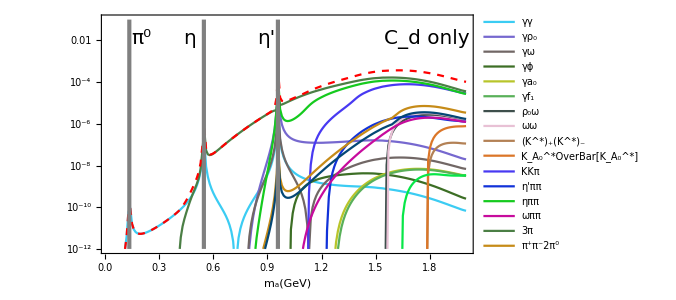

```mathematica
ListLogPlot[resall2[[validlist]],Joined->True,PlotRange->{{0.02,2},{10^-12,10^-1}},PlotStyle->colorlist[[validlist]],ImageSize->500,ImagePadding->{{100,15},{75,15}}  ,
Frame->True,FrameStyle->Directive[{Thickness[0.003],Black,FontFamily->"Avenir",FontSize->12}],FrameTicksStyle->Directive[17,Black],AspectRatio->6/10,
FrameLabel->{Text[Style["m_a(GeV)",20,Black,SingleLetterItalics->True,FontFamily->"Arial"]],Text[Style["
",20,Black,SingleLetterItalics->True,FontFamily->"Arial"]]},
PlotLegends->Placed[LineLegend[Join[colorlist[[validlist]],{Directive[Red,Dashed]}],Join[labels[[validlist]],{"ALL"}]]
,Right]];
ListLogPlot[sum,Joined->True,PlotRange->{All,{10^-12,10^-2}},PlotStyle->Directive[Red,Dashed],
Frame->True,FrameStyle->Directive[{Thickness[0.003],Black,FontFamily->"Avenir",FontSize->12}],FrameTicksStyle->{Directive[Black,12]},
FrameLabel->{"m_a(GeV)","Γ(GeV)"}
];
resfig$=Show[{%%,%,ContourPlot[{x==0.135,x==0.548,x==0.958},{x,0,3},{y,10^-12,10^-1},ContourStyle->Directive[Gray,Thickness[0.006]],ScalingFunctions->{None,"Log"}]},Epilog->{Text[Style[textfig,20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.76,0.9}],Left],Text[Style["π^0",20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.08,0.9}],Left],Text[Style["η",20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.22,0.9}],Left],Text[Style["η'",20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.42,0.9}],Left]}]
```

```mathematica
rr2={"η'ππ"->"etaprimeππ","π^+π^-2π^0"->"πpπm2π0","2π^+2π^-"->"2πp2πm"};
rr2reverse={"etaprimeππ"->"η'ππ","πpπm2π0"->"π^+π^-2π^0","2πp2πm"->"2π^+2π^-"};
```

```mathematica
out$json=Table[(processlist1[[validlist]][[i]]/.rr2)->resall2[[validlist]][[i]],{i,1,Length[processlist1[[validlist]]]}];
```

```mathematica
Export[DirectoryRoutines<>"/res/"<>ToString[xmodel]<>"/Γa.json",out$json];
```

```mathematica
Export[DirectoryRoutines<>"/"<>ToString[xmodel]<>"_res_fig_v1.pdf",resfig$];
```

# Get WZW of axion effective interaction

```mathematica
checkwzw$axiondetails[X_,Y_]:=Block[{listeff},listeff=reseff[X,Y,selectedmodelreplace];Print["The effective couplings of axion-"<>ToString[X]<>"-"<>ToString[Y]<>" up to NLO in isospin-breaking parameter δ is\n" ];
Print[listeff[[1]]];
Print["The coefficients defined in the paper are\n"];
Print["=",listeff[[2,5]]];
Print["=",listeff[[2,1]]];
Print["=",listeff[[2,2]]];
Print["=",listeff[[2,3]]];
Print["=",listeff[[2,4]]];
];
```

```mathematica
Print["Notes: The WZW of axion effective interaction contains the contributions from WZW interaction, mixing with neutral pseudoscalar mesons, the anomalous terms coming from possible chiral rotations which is very complicated. For whom that are interested in the WZW of axion effective interaction details,\n, We provide this section for a convenient check."]
Print["The available spin-1 fields:"]
mesonlist={A[],ρ0[],ω[],ϕ[],a0[],f[],Kstarp[],Kstar0[],Kstarbar[],Kstarm[],ρp[],ρm[],am[],ap[],fs[],KAstarp[],KAstarm[],KAstar0[],KAstarbar[],Z[]}
Print["For example, if we want to see the axion-A[]-A[] in the current "<>ToString[xmodel]<>" Scheme:"]
checkwzw$axiondetails[A[],A[]];
Print["Feel free to check!"]
```

Notes: The WZW of axion effective interaction contains the contributions from WZW interaction, mixing with neutral pseudoscalar mesons, the anomalous terms coming from possible chiral rotations which is very complicated. For whom that are interested in the WZW of axion effective interaction details,
, We provide this section for a convenient check.

The available spin-1 fields:

{A(),ρ0(),ω(),ϕ(),a0(),f(),Kstarp(),Kstar0(),Kstarbar(),Kstarm(),ρp(),ρm(),am(),ap(),fs(),KAstarp(),KAstarm(),KAstar0(),KAstarbar(),Z()}

For example, if we want to see the axion-A[]-A[] in the current Gluon Scheme:

The effective couplings of axion-A[]-A[] up to NLO in isospin-breaking parameter δ is

(e^2 (2 mηpr^2 mπ^2 (Qd^2-Qs^2+Qu^2)+ma^2 (-3 mπ^2 (Qd^2+Qu^2)+2 mη^2 (Qd^2-Qs^2+Qu^2)+mηpr^2 (Qd^2+2 Qs^2+Qu^2))+mη^2 (-3 mηpr^2 (Qd^2+Qu^2)+mπ^2 (Qd^2+2 Qs^2+Qu^2))))/(8 fa (ma^2-mη^2) (ma^2-mηpr^2) π^2)+(e^2 mπ^2 (2 mηpr^2 mπ^2+ma^2 (2 mη^2+mηpr^2-3 mπ^2)+mη^2 (-3 mηpr^2+mπ^2)) (Qd^2-Qu^2) δ)/(8 fa (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ^2) π^2)

The coefficients defined in the paper are

=0

=-(3 cgg e^2 (Qd^2 κd+Qs^2 κs+Qu^2 κu))/(4 fa π^2)

=(3 e^2 (Qd^2-Qu^2))/(4 √2 fπ π^2)

=-(√(3/2) e^2 (Qd^2-2 Qs^2+Qu^2))/(4 fπ π^2)

=-(√3 e^2 (Qd^2+Qs^2+Qu^2))/(4 fπ π^2)

Feel free to check!

```mathematica
checkwzw$axiondetails[Z[],A[]]
```

The effective couplings of axion-Z[]-A[] up to NLO in isospin-breaking parameter δ is

(e^2 (3 cw^2 (2 mηpr^2 mπ^2 (-Qd+Qs+Qu)+mη^2 (3 mηpr^2 (Qd-Qu)+mπ^2 (-Qd-2 Qs+Qu))+ma^2 (3 mπ^2 (Qd-Qu)+mηpr^2 (-Qd-2 Qs+Qu)+2 mη^2 (-Qd+Qs+Qu)))+(ma^2 (-3 mπ^2 (Qd-5 Qu)+2 mη^2 (Qd-Qs-5 Qu)+mηpr^2 (Qd+2 Qs-5 Qu))+mη^2 (-3 mηpr^2 (Qd-5 Qu)+mπ^2 (Qd+2 Qs-5 Qu))+2 mηpr^2 mπ^2 (Qd-Qs-5 Qu)) sw^2))/(48 cw fa (ma-mη) (ma+mη) (ma-mηpr) (ma+mηpr) π^2 sw)-(e^2 mπ^2 (2 mηpr^2 mπ^2+ma^2 (2 mη^2+mηpr^2-3 mπ^2)+mη^2 (-3 mηpr^2+mπ^2)) (3 cw^2 (Qd+Qu)-(Qd+5 Qu) sw^2) δ)/(48 cw fa (ma^2-mη^2) (ma^2-mηpr^2) (ma^2-mπ^2) π^2 sw)

The coefficients defined in the paper are

=(3 e^2 (cw^2+sw^2) (cdl Qd+cdr Qd+csl Qs+csr Qs-cul Qu-cur Qu+2 cgg Qd δd+2 cgg Qs δs-2 cgg Qu δu))/(16 cw fa π^2 sw)

=(cgg (-(2 e^2 sw (3 Qs δs-3 Qu δu+Qd (3 δd+κd)+Qs κs-5 Qu κu))/cw-(6 cw e^2 (Qd (δd-κd)+Qs (δs-κs)+Qu (-δu+κu)))/sw))/(16 fa π^2)

=(e^2 (-3 cw^2 (Qd+Qu)+(Qd+5 Qu) sw^2))/(8 √2 cw fπ π^2 sw)

=(e^2 (3 cw^2 (Qd-2 Qs-Qu)+(-Qd+2 Qs+5 Qu) sw^2))/(8 √6 cw fπ π^2 sw)

=(e^2 (3 cw^2 (Qd+Qs-Qu)-(Qd+Qs-5 Qu) sw^2))/(8 √3 cw fπ π^2 sw)

# *Plot from existing Json Files

```mathematica
Block[{Print=Identity},
(*Parameters and functions*)
NotebookEvaluate[FileNameJoin[{DirectoryRoutines,"alp-models.nb"}]];
];//AbsoluteTiming
```

{0.153562,Null}

Directly plot the figures from previously exported data.

{AA→RGBColor[0.2305913549502483, 0.801945436972624, 0.952006399112787],Aρ0→RGBColor[0.4629029743473536, 0.4063898499069205, 0.8124503470377427],Aω→RGBColor[0.4449312403407435, 0.4048194034938293, 0.39441840852148613],Aϕ→RGBColor[0.23464420610234815, 0.4314867326570686, 0.14698179648585818],Aa0→RGBColor[0.719623343028565, 0.7733978226036808, 0.1634596782709694],Af→RGBColor[0.3495948338269945, 0.6919987524441198, 0.34714485608376644],Afs→RGBColor[0.14805453496242782, 0.11173412484653156, 0.42272524299656067],ρ0ω→RGBColor[0.2423165969667005, 0.3091941407100005, 0.29660461302360197],ρ0ϕ→RGBColor[0.9796848664460693, 0.24785968089164068, 0.290358791122584],ρ0a0→RGBColor[0.8377400709368037, 0.36682752886687453, 0.4596237134047596],ρ0f→RGBColor[0.3314258542633617, 0.10480630888325959, 0.17213232865151729],ρ0fs→RGBColor[0.1568058032847801, 0.35622076722354756, 0.9735339841302757],ωω→RGBColor[0.9099128812517117, 0.7577544040781796, 0.8353734666040578],ωϕ→RGBColor[0.9098629946976331, 0.04128091000410894, 0.36041711492974193],ωa0→RGBColor[0.19202783991777883, 0.5700340118169991, 0.1689484705979165],ωf→RGBColor[0.6012928090766547, 0.48593607102222336, 0.8948381524360451],ωfs→RGBColor[0.07354254127981696, 0.6523578663906355, 0.08404155969922589],ϕϕ→RGBColor[0.31286487918673633, 0.5212689290601833, 0.17752636290032986],ϕa0→RGBColor[0.8666379025883224, 0.07156550701981979, 0.7119530745268012],ϕf→RGBColor[0.16784495019478318, 0.6961501478466396, 0.3821443828218283],ϕfs→RGBColor[0.5575075161559171, 0.5624833966936729, 0.5024941705363615],a0a0→RGBColor[0.8282763916861713, 0.5846323766015566, 0.39121560128165656],a0f→RGBColor[0.2448507139179099, 0.5700135807771898, 0.2842775697930173],a0fs→RGBColor[0.7082215900144648, 0.46583646187172056, 0.8270571973019456],ff→RGBColor[0.6919945672419328, 0.24795493543448854, 0.8896042409465574],ffs→RGBColor[0.03376863487358772, 0.2163597870800782, 0.35905209807057603],fsfs→RGBColor[0.8855240291921069, 0.1823129090389095, 0.8182323647365763],KstarpKstarm→RGBColor[0.7020402531062042, 0.5041117966804471, 0.3325745634852437],Kstar0Kstarbar→RGBColor[0.7149001000055881, 0.5416454256514178, 0.9000954876305018],KAstarpKAstarm→RGBColor[0.33727577141734755, 0.34109281803233316, 0.17303673601451708],KAstar0KAstarbar→RGBColor[0.8582740143371348, 0.46404056542269534, 0.15692140148135114],amap→RGBColor[0.518910442916485, 0.581011782942811, 0.658272205654306],KKπ→RGBColor[0.28131699369186336, 0.22414773272430422, 0.9485174417611257],η'ππ→RGBColor[0.0659276334285499, 0.19549814725929227, 0.8501330421097801],ηππ→RGBColor[0.08375563405889452, 0.7935157006078695, 0.11687427811507334],ωππ→RGBColor[0.7804741437778377, 0.04320429145675764, 0.6143422812671333],3π→RGBColor[0.2960251217815453, 0.4985785765680306, 0.2705099971657394],π^+π^-2π^0→RGBColor[0.7763647147715438, 0.5461072957278517, 0.09246515965420943],2π^+2π^-→RGBColor[0.01515942488076627, 0.27784338668988773, 0.46062283799686154],3η→RGBColor[0.026477436165762924, 0.904788290658253, 0.28160355353986044]}

{AA→γγ,Aρ0→γρ_0,Aω→γω,Aϕ→γϕ,Aa0→γa_0,Af→γf_1,Afs→γf_s,ρ0ω→ρ_0ω,ρ0ϕ→ρ_0ϕ,ρ0a0→ρ_0a_0,ρ0f→ρ_0f_1,ρ0fs→ρ_0f_s,ωω→ωω,ωϕ→ωϕ,ωa0→ωa_0,ωf→ωf_1,ωfs→ωf_s,ϕϕ→ϕϕ,ϕa0→ϕa_0,ϕf→ϕf_1,ϕfs→ϕf_s,a0a0→a_0a_0,a0f→a_0f_1,a0fs→a_0f_s,ff→f_1f_1,ffs→f_1f_s,fsfs→f_sf_s,KstarpKstarm→(K^*)_+(K^*)_-,Kstar0Kstarbar→K_0^*OverBar[K_0^*],KAstarpKAstarm→(K_A^*)_+(K_A^*)_-,KAstar0KAstarbar→K_A_0^*OverBar[K_A_0^*],amap→a^+a^-,KKπ→KKπ,η'ππ→η'ππ,ηππ→ηππ,ωππ→ωππ,3π→3π,π^+π^-2π^0→π^+π^-2π^0,2π^+2π^-→2π^+2π^-,3η→3η}

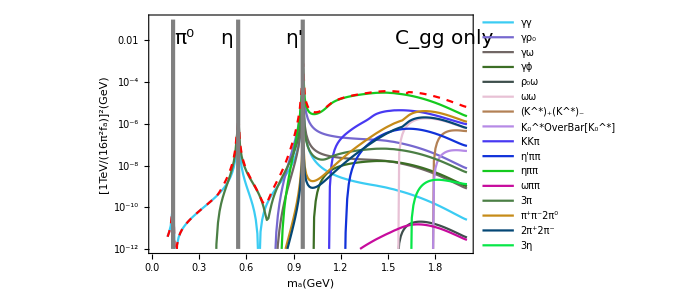

```mathematica
Print["Directly plot the figures from previously exported data."]
DirectoryRoutines=FileNameJoin[{NotebookDirectory[],"notebooks"}];
colorlist={RGBColor[0.2305913549502483, 0.801945436972624, 0.952006399112787],RGBColor[0.4629029743473536, 0.4063898499069205, 0.8124503470377427],RGBColor[0.4449312403407435, 0.4048194034938293, 0.39441840852148613],RGBColor[0.23464420610234815, 0.4314867326570686, 0.14698179648585818],RGBColor[0.719623343028565, 0.7733978226036808, 0.1634596782709694],RGBColor[0.3495948338269945, 0.6919987524441198, 0.34714485608376644],RGBColor[0.14805453496242782, 0.11173412484653156, 0.42272524299656067],RGBColor[0.2423165969667005, 0.3091941407100005, 0.29660461302360197],RGBColor[0.9796848664460693, 0.24785968089164068, 0.290358791122584],RGBColor[0.8377400709368037, 0.36682752886687453, 0.4596237134047596],RGBColor[0.3314258542633617, 0.10480630888325959, 0.17213232865151729],RGBColor[0.1568058032847801, 0.35622076722354756, 0.9735339841302757],RGBColor[0.9099128812517117, 0.7577544040781796, 0.8353734666040578],RGBColor[0.9098629946976331, 0.04128091000410894, 0.36041711492974193],RGBColor[0.19202783991777883, 0.5700340118169991, 0.1689484705979165],RGBColor[0.6012928090766547, 0.48593607102222336, 0.8948381524360451],RGBColor[0.07354254127981696, 0.6523578663906355, 0.08404155969922589],RGBColor[0.31286487918673633, 0.5212689290601833, 0.17752636290032986],RGBColor[0.8666379025883224, 0.07156550701981979, 0.7119530745268012],RGBColor[0.16784495019478318, 0.6961501478466396, 0.3821443828218283],RGBColor[0.5575075161559171, 0.5624833966936729, 0.5024941705363615],RGBColor[0.8282763916861713, 0.5846323766015566, 0.39121560128165656],RGBColor[0.2448507139179099, 0.5700135807771898, 0.2842775697930173],RGBColor[0.7082215900144648, 0.46583646187172056, 0.8270571973019456],RGBColor[0.6919945672419328, 0.24795493543448854, 0.8896042409465574],RGBColor[0.03376863487358772, 0.2163597870800782, 0.35905209807057603],RGBColor[0.8855240291921069, 0.1823129090389095, 0.8182323647365763],RGBColor[0.7020402531062042, 0.5041117966804471, 0.3325745634852437],RGBColor[0.7149001000055881, 0.5416454256514178, 0.9000954876305018],RGBColor[0.33727577141734755, 0.34109281803233316, 0.17303673601451708],RGBColor[0.8582740143371348, 0.46404056542269534, 0.15692140148135114],RGBColor[0.518910442916485, 0.581011782942811, 0.658272205654306],RGBColor[0.28131699369186336, 0.22414773272430422, 0.9485174417611257],RGBColor[0.0659276334285499, 0.19549814725929227, 0.8501330421097801],RGBColor[0.08375563405889452, 0.7935157006078695, 0.11687427811507334],RGBColor[0.7804741437778377, 0.04320429145675764, 0.6143422812671333],RGBColor[0.2960251217815453, 0.4985785765680306, 0.2705099971657394],RGBColor[0.7763647147715438, 0.5461072957278517, 0.09246515965420943],RGBColor[0.01515942488076627, 0.27784338668988773, 0.46062283799686154],RGBColor[0.026477436165762924, 0.904788290658253, 0.28160355353986044]};
labels={"γγ","γρ_0","γω","γϕ","γa_0","γf_1","γf_s","ρ_0ρ_0","ρ_0ω","ρ_0ϕ","ρ_0a_0","ρ_0f_1","ρ_0f_s","ωω","ωϕ","ωa_0","ωf_1","ωf_s","ϕϕ","ϕa_0","ϕf_1","ϕf_s","a_0a_0","a_0f_1","a_0f_s","f_1f_1","f_1f_s","f_sf_s","(K^*)_+(K^*)_-","K_0^*OverBar[K_0^*]","ρ^+ρ^-","(K_A^*)_+(K_A^*)_-","K_A_0^*OverBar[K_A_0^*]","a^+a^-","KKπ","η'ππ","ηππ","ωππ","3π","π^+π^-2π^0","2π^+2π^-","3η"};
pos={Position[labels,"ρ_0ρ_0"][[1]],Position[labels,"ρ^+ρ^-"][[1]]};
labels=Delete[labels,pos];
processlist={"3π^0","π^+π^-π^0","2π^+2π^-","π^+π^-2π^0","η2π^0","ηπ^+π^-","η'π^+π^-","η'2π^0","3η","γπ^+π^-","K^0(K̄)^0π^0","K^+K^-π^0","K^+(K̄)^0π^-","K^-K^0π^+","ωπ^+π^-","AA","Aρ0","Aω","Aϕ","Aa0","Af","Afs","ρ0ρ0","ρ0ω","ρ0ϕ","ρ0a0","ρ0f","ρ0fs","ωω","ωϕ","ωa0","ωf","ωfs","ϕϕ","ϕa0","ϕf","ϕfs","a0a0","a0f","a0fs","ff","ffs","fsfs","KstarpKstarm","Kstar0Kstarbar","ρpρm","KAstarpKAstarm","KAstar0KAstarbar","amap","2G"};
processlist1=Delete[Join[processlist[[16;;-2]],{"KKπ","η'ππ","ηππ","ωππ","3π","π^+π^-2π^0","2π^+2π^-","3η"}],pos];
colorreplace=Table[processlist1[[i]]->colorlist[[i]],{i,1,Length[processlist1]}]
labelreplace=Table[processlist1[[i]]->labels[[i]],{i,1,Length[processlist1]}]
xmodel=ModelSelector1;
textfig=Switch[xmodel,"Gluon","C_gg only","cQ","C_Q only","cd","C_d only"];
rr2={"η'ππ"->"etaprimeππ","π^+π^-2π^0"->"πpπm2π0","2π^+2π^-"->"2πp2πm"};
rr2reverse={"etaprimeππ"->"η'ππ","πpπm2π0"->"π^+π^-2π^0","2πp2πm"->"2π^+2π^-"};
data=Import[DirectoryRoutines<>"/res/"<>ToString[xmodel]<>"/Gamma_a.json"];
labelstemp=data[[All,1]]//.Join[labelreplace,rr2reverse];
colorstemp=data[[All,1]]//.Join[colorreplace,rr2reverse];
sum=Table[{data[[1,2,j,1]],Sum[If[Position[data[[i,2,All,1]],data[[1,2,j,1]]]=!={},data[[i,2,Position[data[[i,2,All,1]],data[[1,2,j,1]]][[1,1]],2]],0],{i,1,Length[data]}]},{j,1,Length[data[[1,2]]]}];
ListLogPlot[data[[All,2]],Joined->True,PlotRange->{{0.02,2},{10^-12,10^-1}},PlotStyle->colorstemp,ImageSize->500,ImagePadding->{{110,15},{75,15}}  ,
Frame->True,FrameStyle->Directive[{Thickness[0.003],Black,FontFamily->"Avenir",FontSize->12}],FrameTicksStyle->Directive[17,Black],AspectRatio->6/10,
FrameLabel->{Text[Style["m_a(GeV)",20,Black,SingleLetterItalics->True,FontFamily->"Arial"]],Text[Style["TemplateBox[<|\"boxes\" -> FormBox[SubscriptBox[\"Γ\", RowBox[{StyleBox[\"a\", \"TI\"], \"→\", StyleBox[\"X\", \"TI\"]}]], TraditionalForm], \"errors\" -> {}, \"input\" -> \"\\\\Gamma_{a\\\\to X}\", \"state\" -> \"Boxes\"|>,\"TeXAssistantTemplate\"][1TeV/(16π^2f_a)]^2(GeV)
",18,Black,SingleLetterItalics->True,FontFamily->"Arial"]]},
PlotLegends->Placed[LineLegend[Join[colorstemp,{Directive[Red,Dashed]}],Join[labelstemp,{"ALL"}]]
,Right]];
ListLogPlot[sum,Joined->True,PlotRange->{All,{10^-12,10^-2}},PlotStyle->Directive[Red,Dashed],
Frame->True,FrameStyle->Directive[{Thickness[0.003],Black,FontFamily->"Avenir",FontSize->12}],FrameTicksStyle->{Directive[Black,12]},
FrameLabel->{"m_a(GeV)","Γ(GeV)"}
];
resfig$=Show[{%%,%,ContourPlot[{x==0.135,x==0.548,x==0.958},{x,0,3},{y,10^-12,10^-1},ContourStyle->Directive[Gray,Thickness[0.006]],ScalingFunctions->{None,"Log"}]},Epilog->{Text[Style[textfig,20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.76,0.9}],Left],Text[Style["π^0",20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.08,0.9}],Left],Text[Style["η",20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.22,0.9}],Left],Text[Style["η'",20,Black,SingleLetterItalics->False,FontFamily->"Arial"],Scaled[{0.42,0.9}],Left]}]
Export[DirectoryRoutines<>"/"<>ToString[xmodel]<>"_res_fig_v1.pdf",resfig$];
```